# 包络线

### 出自

### https://twitter.com/graveolens/status/1550347263146352642?s=20&t=-beDh-cq22HlwDfvMfCQOQ

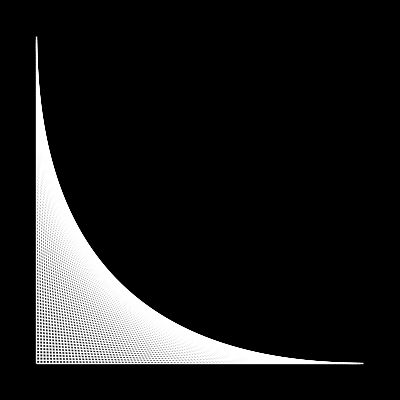

```mathematica
Show[Table[Graphics[{RGBColor[1,1,1],Line[{{0,1-n/100},{n/100,0}}]}],{n,0,100}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Background->Black]
```

### 我的简化版

```mathematica
Graphics[{White,Line[Table[{{0,1-n/100},{n/100,0}},{n,0,100}]]},Background->Black,PlotRange->{{0,1},{0,1}}]
```

-Graphics-

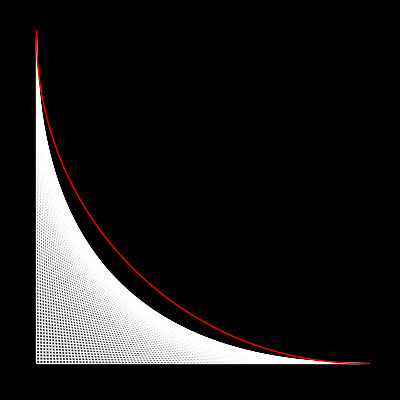

```mathematica
Graphics[{White,Line[Table[{{0,1-n/100},{n/100,0}},{n,0,100}]],Red,Circle[{1,1},1]},Background->Black,PlotRange->{{0,1},{0,1}}]
```

### 那么如何得到包络线的方程呢？

```mathematica
DSolveValue[{f'[x]==(1-x)/-x,f[1]==0},f[x],{x,0,1}]
```

-1+x-Log[x]

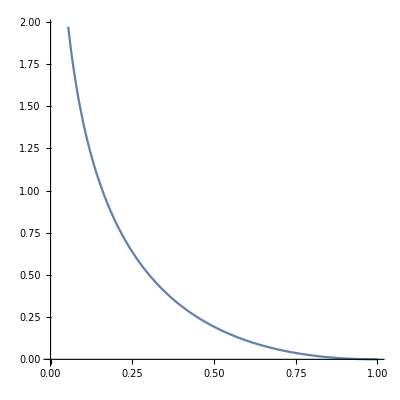

```mathematica
Plot[x-Log[x]-1,{x,0,1},AspectRatio->1]
```

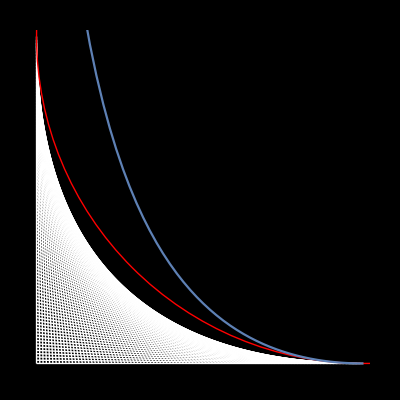

```mathematica
Show[-Graphics-,Plot[x-Log[x]-1,{x,0,1}]]
```

```mathematica
Manipulate[Show[-Graphics-,ContourPlot[Abs[x-1]^a+Abs[y-1]^a==1,{x,0,1},{y,0,1}]],{a,1,5}]
```

### 很接近了，但还不是

```mathematica
Manipulate[Show[-Graphics-,ContourPlot[Abs[x]^a+Abs[y]^a==1,{x,0,1},{y,0,1}]],{{a,1},0.01,5}]
```

### 好像猜对了，看起来相当吻合

```mathematica
Integrate[(3 x^3-x^2+2x-4)/(√(x^2-3x+2)),{x,0,1}]
```

1/8 (-101 √2+135 ArcCoth[√2])

```mathematica
N[1/8 (-101 √2+135 ArcCoth[√2])]
```

-2.98127